```mathematica
(* ENERGY CONDITIONS *)
p[rho_,r_] = rho[r] +r/(n+2)D[rho[r],r] 
fNULL[rho_,r_] = rho[r] + p[rho,r]
fSTRONG[rho_,r_] = (2+n) p[rho,r]
fDOM[rho_,r_] = rho[r]-Abs[ p[rho,r] ]
```

rho[r]+(r rho'[r])/(2+n)

2 rho[r]+(r rho'[r])/(2+n)

(2+n) (rho[r]+(r rho'[r])/(2+n))

-Abs[rho[r]+(r rho'[r])/(2+n)]+rho[r]

```mathematica
ρ[H_] :=Function[r, H'[r]/r^(2+n)]
```

```mathematica
Holo[r_] = r^(2+n)/(r^(2+n)+1)
Halpha[r_] = r^(3+n)/((r^α+1/2)^((3+n)/α))
```

r^(2+n)/(1+r^(2+n))

r^(3+n) (1/2+r^α)^(-(3+n)/α)

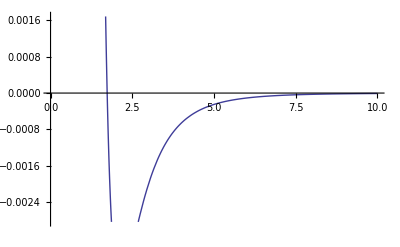

```mathematica
Plot[
fNULL[ρ[Holo],r]/.{n-> 0},
{r,0,10}
]
```